# Rotating star

Author : Martin Horvat, June 2016

```mathematica
Clear[Omega];
Omega[x_,y_,z_,omega_]:=1/Sqrt[x^2+y^2+z^2]+1/2 omega^2(x^2+y^2)
```

```mathematica
Clear[DOmega];
DOmega[x_,y_,z_,omega_]=D[Omega[x,y,z,omega],{{x,y,z}}]
```

{omega^2 x-x/((x^2+y^2+z^2)^(3/2)),omega^2 y-y/((x^2+y^2+z^2)^(3/2)),-z/((x^2+y^2+z^2)^(3/2))}

```mathematica
Simplify[DOmega[0,0,1/Omega0,omega],Omega0>0]
```

{0,0,-Omega0^2}

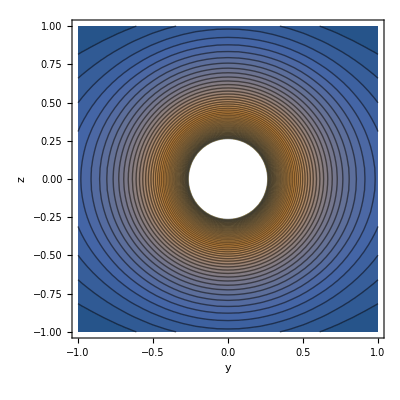

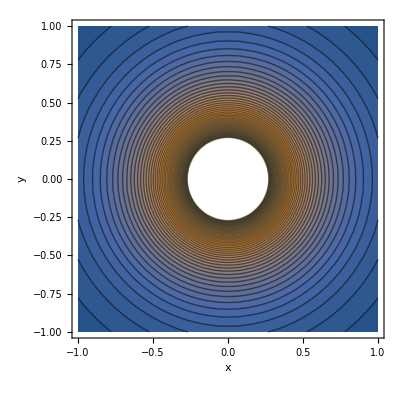

```mathematica
ContourPlot[Omega[0,y,z,0.5],{y,-1,1},{z,-1,1},Contours->50,AxesLabel->{"y","z"}]
ContourPlot[Omega[x,y,0,0.5],{x,-1,1},{y,-1,1},Contours->50,AxesLabel->{"x","y"}]
```

```mathematica
v[s_,b_]:= Sqrt[-s(1-b*s)^2+1]/(1-b*s);
dvds[s_,b_]=FullSimplify[D[v[s,b],s]]
```

(-1+b (2+s (3+b s (-3+b s))))/(2 (-1+b s)^2 √(1-s (-1+b s)^2))

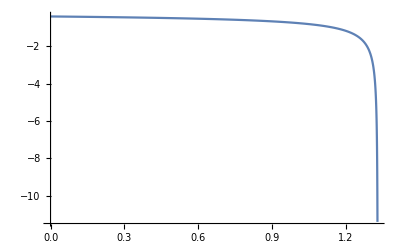

```mathematica
Block[{s0,u0,b},
b=0.1;
u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];
s0=u0*u0;
Plot[dvds[s,b],{s,0,s0*0.999},PlotRange->All]
]
```

```mathematica
Block[{b,s,s0,u0,u},
b=0.0001;

u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];

s0=u0*u0;

NIntegrate[{4Pi*Sqrt[s*dvds[s,b]^2+1/4],-2Pi*s*dvds[s,b]},{s,0,s0}]
]
```

{12.568,4.18963}

```mathematica
1/Abs[x]+1/2w2 x^2
```